## Numerical Integration (Quadrature)

One strategy in developing formulas for numerical integration is similar to that for numerical differentiation.  We fit a polynomial approximation through points of the function and then integrate this polynomial approximation to the function.  If the points are equispaced then the familiar Newton-Gregory forward polynomial is a convenient place to start

	∫_a^b f(x)ⅆx=∫_a^b P_n(x_s)ⅆx
	
Of course, the result will not be exact because the polynomial is not identical to f(x).  Therefore, we have an error expression of the form:

	Error=∫_a^b (s
n+1)h^(n+1)f^(n+1)(ξ)ⅆx
	
If the interval of integration (a,b) matches the range of fit of the polynomial, (x_0,x_n) we get what are called the Newton-Cotes formulas, a set of integration rules corresponding to the varying degrees of the interpolation polynomial.  The first three, should look very familiar shortly.

The utility of numerical integration extends beyond the need to integrate a function known only as tabular data.  Many times, either because we are lazy, the problem is too difficult, or the function simply has no closed form solution we use numerical integration to approximate the integral of analytic functions as well.  The process of numerical integration is often called quadrature.

◀     |     ▶

## Newton-Cotes Formulas

Let us develop three important Newton-Cotes formulas.  During the integration, we will need to change the variable of integration from x to s since our polynomials were expressed in terms of s.  Observe that ⅆx=hⅆs.

For n=1

	((∫_x_0^x_1 f(x)ⅆx=∫_x_0^x_1 (f_0+s Δ f_0)ⅆx=h∫_(s=0)^(s=1) (f_0+s Δ f_0)ⅆs
=h f_0 s])_0^1+h Δ f_0 s^2/2])_0^1=h (f_0+1/2 Δ f_0)
	          = h/2[2 f_0+(f_1-f_0)]=h/2(f_0+f_1)
	
	(Error = ∫_x_0^x_1 (s(s-1))/2 h^2 f''(ξ)ⅆx=h^3 f''(ξ_1)∫_0^1 (s^2-s)/2 ⅆs
             =h^3 f''(ξ_1)(s^3/6-s^2/4)])_0^1=-1/12 h^3 f''(ξ_1),    x_0≤ ξ_1≤ x_1
	
For n=2

	(((∫_x_0^x_2 f(x)ⅆx=∫_x_0^x_2 (f_0+s Δ f_0+(s(s-1))/2 Δ^2 f_0)ⅆx
=h∫_0^2 (f_0+s Δ f_0+(s(s-1))/2 Δ^2 f_0)ⅆs
=h f_0 s])_0^2+h Δ f_0 s^2/2])_0^2+h Δ^2 f_0(s^3/6-s^2/4)])_0^2
                                   =h (2 f_0+2Δ f_0+1/3 Δ^2 f_0)=h/3(f_0+4 f_1+f_2)

Omitting the details of the integration we find the error to be
	
	Error=-1/90 h^5 f''''(ξ_1),    x_0≤ ξ_1≤ x_2
	
And finally for n=3, omitting details we have

	∫_x_0^x_3 f(x)ⅆx=∫_x_0^x_3 P_3(x_s)ⅆx=(3h)/8(f_0+3 f_1+3 f_2+f_3)
	
and 

	Error=-3/80 h^5 f''''(ξ_1),   x_0≤ ξ_1≤x_3

◀     |     ▶

## Summary of Newton-Cotes formulas

∫_x_x_0^x_1 f(x)ⅆx=h/2(f_0+f_1)-1/12 h^3 f''(ξ)
∫_x_x_0^x_2 f(x)ⅆx=h/3(f_0+4 f_1+f_2)-1/90 h^5 f''''(ξ)
∫_x_x_0^x_3 f(x)ⅆx=(3h)/8(f_0+3 f_1+3 f_2+f_3)-3/80 h^5 f''''(ξ)
	
Notice that for both n=2 and n=3 the error terms are O(h^5).  This means that the error of integration using a quadratic is similar to the integral using a cubic.  Also notice that the quadratic's coefficient (-1/90) is smaller than the coefficient for the cubic (-3/80).  The formula based on the quadratic is unexpectedly accurate.  This phenomenon is true of all the even-order Newton-Cotes formulas;  each has an order of h in its error term that is the same as for the formula of the next higher order.  This suggests that the even-order rules are especially useful.

◀     |     ▶

## Trapezoid Rule

The first Newton-Cotes formula, based on approximating f(x) on (x_0,x_1) by a straight line, is called the trapezoid rule.

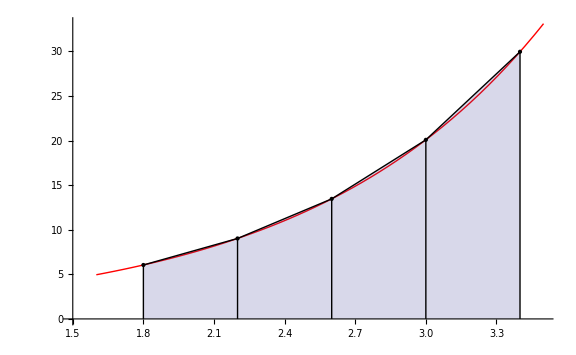

```mathematica
plot1=Plot[Exp[x],{x,1.6,3.5},AxesOrigin->{1.5,0},PlotStyle->{Red},ImageSize->Large];
data=Table[{x,Exp[x]},{x,1.8,3.4,0.4}];
plot2=ListPlot[data,AxesOrigin->{1.5,0}, Filling->Axis,Joined->True,PlotStyle->{Thick,Black},ImageSize->Large];
plot3=ListPlot[data,AxesOrigin->{1.5,0}, Filling->Axis,PlotStyle->{Thick,Black},FillingStyle->{Black},ImageSize->Large];
Show[plot1,plot2,plot3,ImageSize->Large]
```

If we wish to apply the formula for an extended region (more than one interval) of equispaced points we have

	∫_x_i^(x_(i+1)) f(x)ⅆx=(f(x_i)+f(x_(i+1)))/2(Δ x)=h/2(f_i+f_(i+1))

	
For (a,b) subdivided into sub intervals of size h.

	∫_a^b f(x)ⅆx=∑_(i=1)^n h/2(f_i+f_(i+1))=h/2(f_1+f_2+f_2+f_3+f_3+…+f_n+f_(n+1))

∫_a^b f(x)ⅆx=h/2(f_1+2 f_2+…+2 f_n+f_(n+1))
	
This is known as extended trapezoid rule.  Recalling from the error of Newton-Cotes formula we have the local error (the error for a single step) for trapezoid rule as

	Local Error = -1/12 h^3 f''(ξ_1),       x_0≤ ξ_1≤ x_1
	
But we normally apply the trapezoid rule to a series of sub intervals, so the global error would be something like

	Global Error = -1/12h^3[f''(ξ_1)+f''(ξ_2)+…+f''(ξ_n)]
	
If we assume that f''(x) is continuous on (a,b), there is some value of x in (a,b), say x=ξ at which the value of [f''(ξ_1)+f''(ξ_2)+…+f''(ξ_n)]=n f''(ξ).  Then since n h=b-a we have

	Global Error = -1/12 h^3 f''(ξ)=-(b-a)/12 h^2 n f''(ξ)=O(h^2)

◀     |     ▶

## Simpson's rules

The Newton-Cotes formulas based on quadratic and cubic polynomials are widely used.  They are typically known as Simpson's rules.  The second-degree Newton-Cotes formula integrates a quadratic over 2 Δ x intervals that are of uniform width.  Repeating from earlier:

	∫_x_0^x_2 f(x)ⅆx=h/3(f_0+4 f_1+f_2)-h^5/90 f''''(ξ),    x_0≤ ξ≤ x_2
	
This is the popular Simpson's 1/3 rule, which has a local error of O(h^5). If we apply this to a succession of pairs of intervals to evaluate ∫_a^b f(x)ⅆx, we get

	∫_a^b f(x)ⅆx=h/3(f_1+4 f_2+2 f_3+4 f_4+2 f_5+…+2 f_(n-1)+4 f_n+f_(n+1))-(b-a)/180 h^4 f''''(ξ),    x_1≤ ξ≤x_(n+1)
	
Below is a plot which illustrates the idea of Simpson's 1/3rule.  Since we integrate over two intervals each time, we require that the data is subdivided into an even number of intervals.

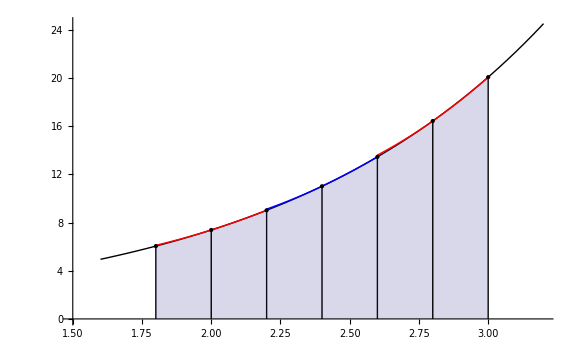

```mathematica
plot1=Plot[Exp[x],{x,1.6,3.2},AxesOrigin->{1.5,0},PlotStyle->{Black},ImageSize->Large];
data=Table[{x,Exp[x]},{x,1.8,3.2,0.2}];
panel1=Fit[Take[data,{2,4}],{1,x,x^2},x];
panel2=Fit[Take[data,{4,6}],{1,x,x^2},x];
panel3=Fit[Take[data,{6,8}],{1,x,x^2},x];
plot2=Plot[panel1,{x,1.8,2.2},AxesOrigin->{1.5,0},PlotStyle->{Thickness[0.0018],Red},Filling->Axis];
plot3=Plot[panel2,{x,2.2,2.6},AxesOrigin->{1.5,0},PlotStyle->{Thickness[0.0018],Blue},Filling->Axis];
plot4=Plot[panel3,{x,2.6,3.0},AxesOrigin->{1.5,0},PlotStyle->{Thickness[0.0018],Red},Filling->Axis];
plot5=ListPlot[Take[data,{1,7}],AxesOrigin->{1.5,0}, Filling->Axis,PlotStyle->{Thick,Black},FillingStyle->{Black},ImageSize->Large];
Show[plot1,plot2,plot3,plot4,plot5,ImageSize->Large]
```

◀     |     ▶

## Simpson's rules (contd.)

The third Newton-Cotes formula that finds frequent use is obtained by integrating a cubic interpolation polynomial over its range of fit.  The local rule (from previous slide) is:

	∫_x_0^x_3 f(x)ⅆx=(3h)/8(f_0+3 f_1+3 f_2+f_3)-3/80 h^5 f''''(ξ),    x_0≤ ξ≤ x_3
	
This is Simpson's 3/8 rule, which has a local error of O(h^5). If we apply this to a succession of triplicates of intervals to evaluate ∫_a^b f(x)ⅆx, we get

	∫_a^b f(x)ⅆx=(3h)/8(f_1+3 f_2+3 f_3+2 f_4+3 f_5+3 f_6+…+2 f_(n-2)+3 f_(n-1)+3 f_n+f_(n+1))-(b-a)/80 h^4 f''''(ξ),    x_1≤ ξ≤x_(n+1)
	
Below is a plot which illustrates the idea of Simpson's 3/8rule.  Since we integrate over three intervals each time, we require that the data is subdivided into a number of intervals divisible by three.  But, as we have seen, the order of the global error for both of Simpson's rules is O(h^4) and the coefficient for the 3/8rule is larger.  One might wonder why we would ever use the 3/8 rule, and this is a valid observation.  In practice is often not true that tabulated data is divisible by 2.  In these cases we typically combine the two methods, applying Simpson's 1/3rule to all the data except for the last three intervals in which we pick up with Simpson's 3/8 rule.

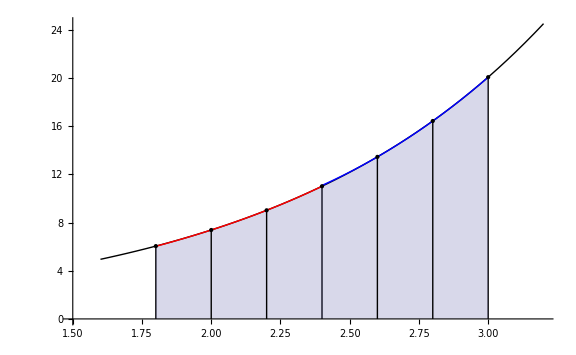

```mathematica
plot1=Plot[Exp[x],{x,1.6,3.2},AxesOrigin->{1.5,0},PlotStyle->{Black},ImageSize->Large];
data=Table[{x,Exp[x]},{x,1.8,3.2,0.2}];
panel1=Fit[Take[data,{2,5}],{1,x,x^2,x^3},x];
panel2=Fit[Take[data,{5,7}],{1,x,x^2,x^3},x];
plot2=Plot[panel1,{x,1.8,2.4},AxesOrigin->{1.5,0},PlotStyle->{Thickness[0.0018],Red},Filling->Axis];
plot3=Plot[panel2,{x,2.4,3.0},AxesOrigin->{1.5,0},PlotStyle->{Thickness[0.0018],Blue},Filling->Axis];
plot5=ListPlot[Take[data,{1,7}],AxesOrigin->{1.5,0}, Filling->Axis,PlotStyle->{Thick,Black},FillingStyle->{Black},ImageSize->Large];
Show[plot1,plot2,plot3,plot5,ImageSize->Large]
```

◀     |     ▶

## Psuedocode for Simpson's Rule

The following pseudocode is used to approximate the integral I=∫_a^b f(x)ⅆx using Simpson's 1/3rule.  The same approach can me used with minor modifications for Trapezoid rule and Simpson's 3/8rule.

Step 1.  Set h=(b-a)/n  where n is the number of intervals in the larger interval (a,b)
Step 2.  Set XI0=f(a)+f(b)
Step 3.  Set XI1=0
Step 4.  Set XI2=0
Step 5.  For i=1,…, n-1 do Steps 6-9
	Step 6.  Set X=a+i h
	Step 7.  If i is even do Step 8.
			Step 8.  Set XI2=XI2+f(X)
	             Else do Step 9
	             	Step 9.  Set XI1=XI1+f(X)
	             	
	Step 10.  Set XI=h (XI0+2XI2+4XI1)/3

◀     |     ▶

## Other ways of deriving integration formulas

We can use the symbolic tools we developed for deriving differentiation formulas in the last lecture in the exact same way for integration formulas.  This is a somewhat straightforward procedure, therefore it will be omitted here in favor of another technique.  This method may be called the method of undetermined coefficients.  We express the formula as a sum of n+1 terms with unknown coefficients, and then evaluate the coefficients by requiring that the formula be exact for all polynomials of degree n or less.  Let's look at an example where we express the integral as a weighted sum of three equispaced function values over the limits of integration.

	∫_-1^1 f(x)ⅆx=a f(-1)+b f(0) +c f(1)
	
Since the formula contains three terms, we can require it to be correct for all polynomials of degree 2 or less.  This process is illustrated below:

	f(x)=1;           ∫_(=1)^1 1ⅆx=2=a(1)+b(1)+c(1)=a+b+c

f(x)=x;          ∫_-1^1 xⅆx=0=a(-1)+b(0)+c(1)=-a+c

f(x)=x^2          ∫_-1^1 x^2 ⅆx=2/3=a(1)+b(0)+c(1)=a+c
	
Solving these three equations simultaneously gives a=2/3,b=4/3,c=1/3.  Here the spacing was 1, but the integral will be proportional to Δ x=h.  We then get Simpson's 1/3rule:

	∫_-h^h f(x)ⅆx=h[1/3 f(-h)+4/3 f(0)+1/3 f(h)]

◀     |     ▶

## Gaussian Quadrature

The Newton-Cotes formulas for numerical integration were all developed on evenly spaced x-values, this means that the x values were predetermined, possible as a result of experimental data acquisition or by evaluating an explicit known function at equal intervals.  For a Newton-Cotes formula of three terms, then, there were three parameters:  the coefficients (weighting factors) applied to each of the functional values.  A formula with three parameters corresponds to a polynomial of the second degree, one less than the number of parameters.  Gauss observed that if we remove the requirement that the function be evaluated at predetermined x-values, a three term formula will contain six parameters (the x-values are now unknowns, plus the three weights) and should correspond to an interpolation polynomial of degree 5.  Formulas based on  this principle are called Gaussian quadrature formulas.  The can be applied only when f(x) is explicitly known, so that it can be evaluated at any desired value of x.

We will determine the parameters in the simple case of a two-term formula containing four unknown parameters:

	∫_-1^1 f(t)ⅆdt=a f(t_1)+b f(t_2)
	
We use a symmetric interval of integration to simplify the arithmetic and follow the methodology of undetermined coefficients.  We wish to have a formula that is valid for any polynomial of degree 3:

	f(t)=t^3;             ∫_-1^1 t^3 ⅆt=0=a t_1^3+b t_2^3

f(t)=t^2;           ∫_-1^1 t^2 ⅆt=2/3=a t_1^2+b t_2^2

f(t)=t;             ∫_-1^1 tⅆt=0=a t_1+b t_2

f(t)=1;            ∫_-1^1 1ⅆt=2=a+b
	
Multiplying the third equation above by t_1^2, and subtracting from the first, we have

	0=0+b[t_2^3-t_2 t_1^2]=b(t_2)(t_2-t_1)(t_2-t_1)
	
We can satisfy this equation with either b=0, t_2=0, t_1=t_2, t_2=-t_1, but only the last choice is satisfactory.  We then find that:

	a=b=1

t_1=-t_2=√(1/3)=0.5773

∫_-1^1 f(t)ⅆt=f(-0.5773)+f(0.5773)
	
It is quite amazing that by adding these two values of the function gives the exact value for the integral of any cubic polynomial over the interval from -1 to 1.

Now suppose our limits of integration are from a to b instead of -1 to 1.  To use the tabulated Gaussian quadrature parameters developed above we can utilize a change of variables to change the interval of integration back to -1 to 1.  If we let

	x=((b-a)t+b+a)/2 so that ⅆx=((b-a)/2)ⅆt, then
	
	∫_a^b f(x)ⅆx=(b-a)/2∫_-1^1 f(((b-a)t+b+a)/2)ⅆt

◀     |     ▶

## Gaussian Quadrature (contd.)

In the above derivation the coefficients a and b where called weights in the case of 2 points the weights where equal to 1 therefore they did not show up in the rest final equation, but if we extend Gauss quadrature beyond 2 terms.  The formula is then given by:

	∫_-1^1 f(t)ⅆt=∑_(i=1)^n w_i f(t_i),   for n points.
	
This formula is exact for functions f(t) that are polynomials of degree 2n-1 or less!  If we extend the derivation for the 2-point formula, for each n we obtain a system of 2n equations:

	w_1 t_1^k+…+w_n t_n^k=Piecewise[{{0, for k=1,3,5,…,2n-1}, {2/(k+1), for k=0,2,4,…,2n-2}}]
	
However, the system of equations we get by writing f(t) as a succession of polynomials is tedious to solve in a straightforward manner.  Techniques that recognize properties of Legendre polynomials can be utilized to simply the solution and this outlined in many texts.  For our purposes we will just utilize the tabulated values that many others have already solved for us.  Tables can be found that give values for up to 200-term formulas, below is a table that includes just a few:

	Number of terms | Values of t | Weighting
Factor | Valid up to
degree
2 | -0.57735027 | 1.0 | 3
  | 0.57735027 | 1.0 |  
3 | -0.77459667 | 0.555555555 | 5
  | 0.0 | 0.888888889 |  
  | 0.77459667 | 0.555555555 |  
4 | -0.86113631 | 0.34785485 | 7
  | -0.33998104 | 0.65214515 |  
  | 0.33998104 | 0.65214515 |  
  | 0.86113631 | 0.34785485 |  
5 | -0.90617975 | 0.23692689 | 9
  | -0.53846931 | 0.47862867 |  
  | 0.0 | 0.56888889 |  
  | 0.53846931 | 0.47862867 |  
  | 0.90617975 | 0.23692689 |

◀     |     ▶

## Gaussian quadrature for multiple integrals

To apply Gaussian quadrature to 

	∫_a^b ∫_(c(x))^(d(x)) f(x,y)ⅆyⅆx
	
we first transform, for each x in [a,b], the interval [c(x),d(x)] to [-1,1] and apply Gauss quadrature for the inside integral.  This results in the following:

	∫_a^b ∫_(c(x))^(d(x)) f(x,y)ⅆyⅆx≈∫_a^b (d(x)-c(x))/2∑_(i=1)^n w_i f(x,((d(x)-c(x))t_i+d(x)+c(x))/2)ⅆx
	
Now the interval [a,b] is transformed to [-1,1] and Gauss quadrature is applied:

	∫_a^b ∫_(c(x))^(d(x)) f(x,y)ⅆyⅆx≈(b-a)/2(d(x)-c(x))/2∑_(j=1)^m ∑_(i=1)^n w_i W_j f(((b-a)s_j+b+a)/2,((d(x)-c(x))t_i+d(x)+c(x))/2)
	
where x=((b-a)s_j+b+a)/2. 

We'll illustrate this using Mathematica for the arithmetic; we wish to evaluate the function:

	∫_0^1 ∫_0^(x^2+1) x yⅆyⅆx
	
After converting the limits of integration we have:

	1/4∫_-1^1 ∫_-1^1 (s+1)/2[((x^2(s)+1)^2 t+(x^2(s)+1)^2)/2]ⅆtⅆs

Now using Mathematica:

```mathematica
f[s_,t_]:=(s+1)/2(((x^2+1)^2 t+(x^2+1)^2)/2)/.{x->(s+1)/2}
w={0.55555555,0.88888889,0.55555555};
s={-0.77459667,0.0,0.77459667};
W={0.34785485,0.65214515,0.65214515,0.34785485};
t={-0.86113631,-0.33998104,0.33998104,0.86113631};
```

We'll use 3-point quadrature in the x-direction and 4-point quadrature in the y-direction.

```mathematica
J=1/4∑_(i=1)^3 ∑_(j=1)^4 w[[i]]W[[j]]f[s[[i]],t[[j]]]
```

0.583333

Comparing with Mathematica's solution

```mathematica
∫_0^1 ∫_0^(x^2+1) x yⅆyⅆx//N
```

0.583333

◀     |     ▶

## Pseudocode for Gaussian Double Integration

The approximate the integral ∫_a^b ∫_(c(x))^(d(x)) f(x,y)ⅆyⅆx given the function f(x,y), the interval [a,b], and order's m and n of Gauss quadrature desired.

Step 1.  h_1=(b-a)/2
Step 2.  h_2=(b+a)/2
Step 3.  J=0

Step 4.  For i=1,2,..., m do Steps 5-15

	Step 5.  Set JX=0
	Step 6.  x=h_1 s_i+h_2,  where s_i is the i^th root (t value) corresponding to an m-point Gauss quadrature
	Step 7.  d_1=d(x)
	Step 8.  c_1=c(x)
	Step 9.  k_1=(d_1-c_1)/2
	Step 10.  k_2=(d_1+c_1)/2
	
	Step 11.  For j=1,2, …, n do Steps 12-14
	
		Step 12.  Set y=k_1 t_j+k_2, where t_j is the j^th root (t value) corresponding to an n-point Gauss quadrature
		Step 13.  Set Q=f(x,y)
		Step 14.  Set JX=JX+W_j Q, where W_j is the j^th weighted value corresponding to an n-point Gauss quadrature
		
	Step 15.  Set J=J+w_i k_1 JX, where w_i is the i^th weighted value corresponding to an m-point Gauss quadrature
	
Step 16.  J=h_1 J

◀     |     ▶